```mathematica
ithpairo[i0_]:=If[EvenQ[i0],Block[{i=i0/2},{Ceiling[(√(8i+1)+1)/2],i-Floor[(√(8i-7)-1)/2](Floor[(√(8i-7)-1)/2]+1)/2}],Block[{i=(i0+1)/2},{i-Floor[(√(8i-7)-1)/2](Floor[(√(8i-7)-1)/2]+1)/2,Ceiling[(√(8i+1)+1)/2]}]]
pairnumo[{i_,j_}]:=If[i<j,(1+i+1/2(j-3)j)2-1,2(1+j+1/2(i-3)i)]
```

```mathematica
Table[pairnumo[ithpairo[i]],{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
seqnum[s_]:=pairnumo[{Fold[pairnumo[{#1,#2}]&,First[s],Drop[s,1]],Length[s]-1}]
```

```mathematica
Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,3]]],{2}]]]]
```

{1,2,2,1}

```mathematica
Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,4]]],{2}]]]]
```

{1,3,5,3,3,5,3,1}

```mathematica
Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,5]]],{2}]]]]
```

{1,4,9,6,9,16,11,4,4,11,16,9,6,9,4,1}

```mathematica
Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,6]]],{2}]]]]
```

{1,5,14,10,19,35,26,10,14,40,61,35,26,40,19,5,5,19,40,26,35,61,40,14,10,26,35,19,10,14,5,1}

```mathematica
Timing[Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,10]]],{2}]]]]]
```

{9.56783,{1,9,44,36,119,231,196,84,209,621,1006,594,511,819,434,126,251,999,2224,1476,2149,3801,2576,924,799,2151,3026,1674,1001,1449,574,126,209,1041,2896,2064,3871,7119,5264,2016,2731,7779,11804,6756,4949,7581,3556,924,799,2991,6176,3984,5201,9009,5824,2016,1301,3309,4324,2316,1099,1491,476,84,119,711,2356,1764,3961,7449,5804,2316,3871,11259,17594,10206,8009,12501,6166,1674,2149,8361,18056,11844,16451,28839,19144,6756,5201,13689,18694,10206,5599,7911,2906,594,511,2439,6464,4536,8009,14601,10576,3984,4949,13941,20836,11844,8371,12699,5804,1476,1001,3609,7144,4536,5599,9591,6056,2064,1099,2691,3356,1764,701,909,244,36,44,306,1171,909,2356,4494,3629,1491,2896,8514,13529,7911,6464,10206,5191,1449,2224,8766,19241,12699,18056,31794,21319,7581,6176,16434,22759,12501,7144,10206,3881,819,1006,4944,13529,9591,17594,32256,23671,9009,11804,33486,50521,28839,20836,31794,14759,3801,3026,11184,22759,14601,18694,32256,20681,7119,4324,10866,13991,7449,3356,4494,1369,231,196,1134,3629,2691,5804,10866,8371,3309,5264,15246,23671,13689,10576,16434,8009,2151,2576,9954,21319,13941,19144,33486,22121,7779,5824,15246,20681,11259,6056,8514,3079,621,434,2016,5191,3609,6166,11184,8009,2991,3556,9954,14759,8361,5804,8766,3961,999,574,2016,3881,2439,2906,4944,3079,1041,476,1134,1369,711,244,306,71,9,9,71,306,244,711,1369,1134,476,1041,3079,4944,2906,2439,3881,2016,574,999,3961,8766,5804,8361,14759,9954,3556,2991,8009,11184,6166,3609,5191,2016,434,621,3079,8514,6056,11259,20681,15246,5824,7779,22121,33486,19144,13941,21319,9954,2576,2151,8009,16434,10576,13689,23671,15246,5264,3309,8371,10866,5804,2691,3629,1134,196,231,1369,4494,3356,7449,13991,10866,4324,7119,20681,32256,18694,14601,22759,11184,3026,3801,14759,31794,20836,28839,50521,33486,11804,9009,23671,32256,17594,9591,13529,4944,1006,819,3881,10206,7144,12501,22759,16434,6176,7581,21319,31794,18056,12699,19241,8766,2224,1449,5191,10206,6464,7911,13529,8514,2896,1491,3629,4494,2356,909,1171,306,44,36,244,909,701,1764,3356,2691,1099,2064,6056,9591,5599,4536,7144,3609,1001,1476,5804,12699,8371,11844,20836,13941,4949,3984,10576,14601,8009,4536,6464,2439,511,594,2906,7911,5599,10206,18694,13689,5201,6756,19144,28839,16451,11844,18056,8361,2149,1674,6166,12501,8009,10206,17594,11259,3871,2316,5804,7449,3961,1764,2356,711,119,84,476,1491,1099,2316,4324,3309,1301,2016,5824,9009,5201,3984,6176,2991,799,924,3556,7581,4949,6756,11804,7779,2731,2016,5264,7119,3871,2064,2896,1041,209,126,574,1449,1001,1674,3026,2151,799,924,2576,3801,2149,1476,2224,999,251,126,434,819,511,594,1006,621,209,84,196,231,119,36,44,9,1}}

```mathematica
horns=Monitor[Table[Map[Last,Sort[Tally[Map[Boole[Sign[#]==1]&,Map[Differences,Permutations[Range[1,m]]],{2}]]]],{m,1,10}],m]
```

{{1},{1,1},{1,2,2,1},{1,3,5,3,3,5,3,1},{1,4,9,6,9,16,11,4,4,11,16,9,6,9,4,1},{1,5,14,10,19,35,26,10,14,40,61,35,26,40,19,5,5,19,40,26,35,61,40,14,10,26,35,19,10,14,5,1},{1,6,20,15,34,64,50,20,34,99,155,90,71,111,55,15,20,78,169,111,155,272,181,64,50,132,181,99,55,78,29,6,6,29,78,55,99,181,132,50,64,181,272,155,111,169,78,20,15,55,111,71,90,155,99,34,20,50,64,34,15,20,6,1},{1,7,27,21,55,105,85,35,69,203,323,189,155,245,125,35,55,217,477,315,449,791,531,189,155,413,573,315,181,259,99,21,27,133,365,259,477,875,643,245,323,917,1385,791,573,875,407,105,85,315,643,413,531,917,589,203,125,315,407,217,99,133,41,7,7,41,133,99,217,407,315,125,203,589,917,531,413,643,315,85,105,407,875,573,791,1385,917,323,245,643,875,477,259,365,133,27,21,99,259,181,315,573,413,155,189,531,791,449,315,477,217,55,35,125,245,155,189,323,203,69,35,85,105,55,21,27,7,1},{1,8,35,28,83,160,133,56,125,370,595,350,295,470,245,70,125,496,1099,728,1051,1856,1253,448,379,1016,1421,784,461,664,259,56,83,412,1141,812,1513,2780,2051,784,1051,2990,4529,2590,1889,2890,1351,350,295,1100,2261,1456,1889,3268,2107,728,461,1168,1519,812,379,512,161,28,35,208,685,512,1141,2144,1667,664,1099,3194,4985,2890,2261,3526,1735,470,595,2312,4985,3268,4529,7936,5263,1856,1421,3736,5095,2780,1519,2144,785,160,133,632,1667,1168,2051,3736,2701,1016,1253,3526,5263,2990,2107,3194,1457,370,245,880,1735,1100,1351,2312,1457,496,259,632,785,412,161,208,55,8,8,55,208,161,412,785,632,259,496,1457,2312,1351,1100,1735,880,245,370,1457,3194,2107,2990,5263,3526,1253,1016,2701,3736,2051,1168,1667,632,133,160,785,2144,1519,2780,5095,3736,1421,1856,5263,7936,4529,3268,4985,2312,595,470,1735,3526,2261,2890,4985,3194,1099,664,1667,2144,1141,512,685,208,35,28,161,512,379,812,1519,1168,461,728,2107,3268,1889,1456,2261,1100,295,350,1351,2890,1889,2590,4529,2990,1051,784,2051,2780,1513,812,1141,412,83,56,259,664,461,784,1421,1016,379,448,1253,1856,1051,728,1099,496,125,70,245,470,295,350,595,370,125,56,133,160,83,28,35,8,1},{1,9,44,36,119,231,196,84,209,621,1006,594,511,819,434,126,251,999,2224,1476,2149,3801,2576,924,799,2151,3026,1674,1001,1449,574,126,209,1041,2896,2064,3871,7119,5264,2016,2731,7779,11804,6756,4949,7581,3556,924,799,2991,6176,3984,5201,9009,5824,2016,1301,3309,4324,2316,1099,1491,476,84,119,711,2356,1764,3961,7449,5804,2316,3871,11259,17594,10206,8009,12501,6166,1674,2149,8361,18056,11844,16451,28839,19144,6756,5201,13689,18694,10206,5599,7911,2906,594,511,2439,6464,4536,8009,14601,10576,3984,4949,13941,20836,11844,8371,12699,5804,1476,1001,3609,7144,4536,5599,9591,6056,2064,1099,2691,3356,1764,701,909,244,36,44,306,1171,909,2356,4494,3629,1491,2896,8514,13529,7911,6464,10206,5191,1449,2224,8766,19241,12699,18056,31794,21319,7581,6176,16434,22759,12501,7144,10206,3881,819,1006,4944,13529,9591,17594,32256,23671,9009,11804,33486,50521,28839,20836,31794,14759,3801,3026,11184,22759,14601,18694,32256,20681,7119,4324,10866,13991,7449,3356,4494,1369,231,196,1134,3629,2691,5804,10866,8371,3309,5264,15246,23671,13689,10576,16434,8009,2151,2576,9954,21319,13941,19144,33486,22121,7779,5824,15246,20681,11259,6056,8514,3079,621,434,2016,5191,3609,6166,11184,8009,2991,3556,9954,14759,8361,5804,8766,3961,999,574,2016,3881,2439,2906,4944,3079,1041,476,1134,1369,711,244,306,71,9,9,71,306,244,711,1369,1134,476,1041,3079,4944,2906,2439,3881,2016,574,999,3961,8766,5804,8361,14759,9954,3556,2991,8009,11184,6166,3609,5191,2016,434,621,3079,8514,6056,11259,20681,15246,5824,7779,22121,33486,19144,13941,21319,9954,2576,2151,8009,16434,10576,13689,23671,15246,5264,3309,8371,10866,5804,2691,3629,1134,196,231,1369,4494,3356,7449,13991,10866,4324,7119,20681,32256,18694,14601,22759,11184,3026,3801,14759,31794,20836,28839,50521,33486,11804,9009,23671,32256,17594,9591,13529,4944,1006,819,3881,10206,7144,12501,22759,16434,6176,7581,21319,31794,18056,12699,19241,8766,2224,1449,5191,10206,6464,7911,13529,8514,2896,1491,3629,4494,2356,909,1171,306,44,36,244,909,701,1764,3356,2691,1099,2064,6056,9591,5599,4536,7144,3609,1001,1476,5804,12699,8371,11844,20836,13941,4949,3984,10576,14601,8009,4536,6464,2439,511,594,2906,7911,5599,10206,18694,13689,5201,6756,19144,28839,16451,11844,18056,8361,2149,1674,6166,12501,8009,10206,17594,11259,3871,2316,5804,7449,3961,1764,2356,711,119,84,476,1491,1099,2316,4324,3309,1301,2016,5824,9009,5201,3984,6176,2991,799,924,3556,7581,4949,6756,11804,7779,2731,2016,5264,7119,3871,2064,2896,1041,209,126,574,1449,1001,1674,3026,2151,799,924,2576,3801,2149,1476,2224,999,251,126,434,819,511,594,1006,621,209,84,196,231,119,36,44,9,1}}

```mathematica
Table[horns[[i]][[1]],{i,1,10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[horns[[i]][[2]],{i,2,10}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[horns[[i]][[3]],{i,3,10}]
```

{2,5,9,14,20,27,35,44}

```mathematica
Expand[InterpolatingPolynomial[%,m]]
```

(3 m)/2+m^2/2

```mathematica
Table[horns[[i]][[4]],{i,3,10}]
```

{1,3,6,10,15,21,28,36}

```mathematica
Expand[InterpolatingPolynomial[%,m]]
```

m/2+m^2/2

```mathematica
Table[horns[[i]][[5]],{i,4,10}]
```

{3,9,19,34,55,83,119}

```mathematica
Expand[InterpolatingPolynomial[%,m]]
```

(11 m)/6+m^2+m^3/6

```mathematica
Table[horns[[i]][[6]],{i,4,10}]
```

{5,16,35,64,105,160,231}

```mathematica
Expand[InterpolatingPolynomial[%,m]]
```

(8 m)/3+2 m^2+m^3/3

```mathematica
Table[horns[[i]][[7]],{i,4,10}]
```

{3,11,26,50,85,133,196}

```mathematica
Expand[InterpolatingPolynomial[%,m]]
```

(7 m)/6+(3 m^2)/2+m^3/3

```mathematica
Min[horns[[10]]]
```

1

```mathematica
Flatten[Position[horns[[10]],9]]
```

{2,256,257,511}

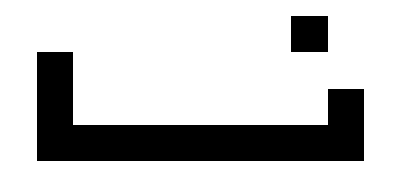

```mathematica
ArrayPlot[Map[PadLeft[IntegerDigits[#,2],9]&,Flatten[Position[horns[[10]],9]]]]
```

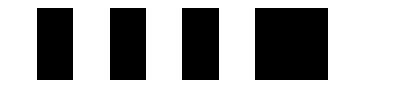

```mathematica
ArrayPlot[Map[PadRight[IntegerDigits[#,2],9]&,Flatten[Position[horns[[10]],50521]]]]
```

```mathematica
><><><>><
```

```mathematica
Sort[DeleteDuplicates[Map[Last,Tally[horns[[10]]]]]]
```

{2,4,8}

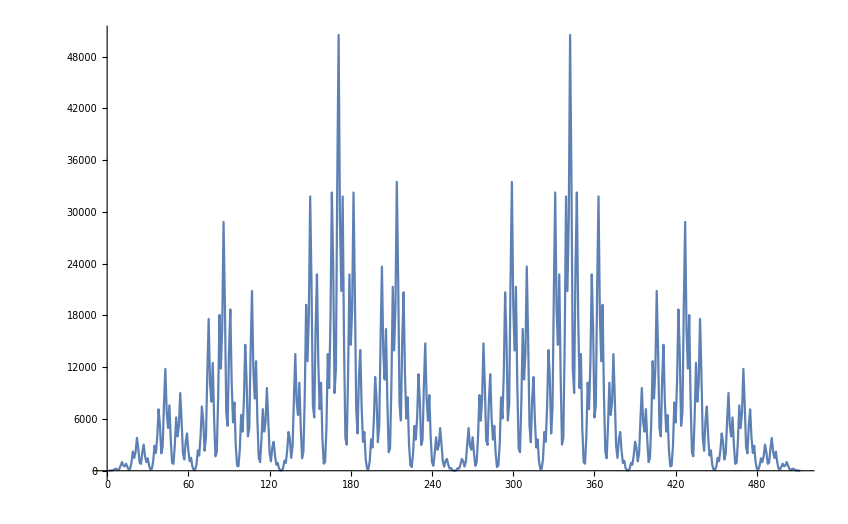

```mathematica
ListPlot[horns[[10]],Joined->True,PlotRange->All]
```

```mathematica
Sort[Tally[Table[Map[Boole[Sign[#]==1]&,Differences[Permute[Range[1,7],RandomPermutation[SymmetricGroup[7]]]]],{w,1,100000}]]]
```

```mathematica
Monitor[Sort[Tally[Table[Map[Boole[Sign[#]==1]&,Differences[Permute[Range[1,7],RandomPermutation[SymmetricGroup[7]]]]],{w,1,100000}]]],w]
```

{{{0,0,0,0,0,0},17},{{0,0,0,0,0,1},145},{{0,0,0,0,1,0},414},{{0,0,0,0,1,1},306},{{0,0,0,1,0,0},649},{{0,0,0,1,0,1},1327},{{0,0,0,1,1,0},996},{{0,0,0,1,1,1},400},{{0,0,1,0,0,0},679},{{0,0,1,0,0,1},1974},{{0,0,1,0,1,0},2990},{{0,0,1,0,1,1},1730},{{0,0,1,1,0,0},1431},{{0,0,1,1,0,1},2148},{{0,0,1,1,1,0},1107},{{0,0,1,1,1,1},278},{{0,1,0,0,0,0},443},{{0,1,0,0,0,1},1549},{{0,1,0,0,1,0},3444},{{0,1,0,0,1,1},2195},{{0,1,0,1,0,0},3082},{{0,1,0,1,0,1},5565},{{0,1,0,1,1,0},3586},{{0,1,0,1,1,1},1216},{{0,1,1,0,0,0},955},{{0,1,1,0,0,1},2625},{{0,1,1,0,1,0},3654},{{0,1,1,0,1,1},1888},{{0,1,1,1,0,0},1076},{{0,1,1,1,0,1},1627},{{0,1,1,1,1,0},594},{{0,1,1,1,1,1},119},{{1,0,0,0,0,0},133},{{1,0,0,0,0,1},590},{{1,0,0,0,1,0},1562},{{1,0,0,0,1,1},1052},{{1,0,0,1,0,0},1982},{{1,0,0,1,0,1},3523},{{1,0,0,1,1,0},2593},{{1,0,0,1,1,1},1000},{{1,0,1,0,0,0},1253},{{1,0,1,0,0,1},3652},{{1,0,1,0,1,0},5330},{{1,0,1,0,1,1},3075},{{1,0,1,1,0,0},2222},{{1,0,1,1,0,1},3416},{{1,0,1,1,1,0},1525},{{1,0,1,1,1,1},363},{{1,1,0,0,0,0},276},{{1,1,0,0,0,1},1110},{{1,1,0,0,1,0},2222},{{1,1,0,0,1,1},1460},{{1,1,0,1,0,0},1764},{{1,1,0,1,0,1},3004},{{1,1,0,1,1,0},1878},{{1,1,0,1,1,1},665},{{1,1,1,0,0,0},361},{{1,1,1,0,0,1},967},{{1,1,1,0,1,0},1220},{{1,1,1,0,1,1},717},{{1,1,1,1,0,0},322},{{1,1,1,1,0,1},422},{{1,1,1,1,1,0},110},{{1,1,1,1,1,1},22}}

```mathematica
Map[Last,%]
```

{17,145,414,306,649,1327,996,400,679,1974,2990,1730,1431,2148,1107,278,443,1549,3444,2195,3082,5565,3586,1216,955,2625,3654,1888,1076,1627,594,119,133,590,1562,1052,1982,3523,2593,1000,1253,3652,5330,3075,2222,3416,1525,363,276,1110,2222,1460,1764,3004,1878,665,361,967,1220,717,322,422,110,22}

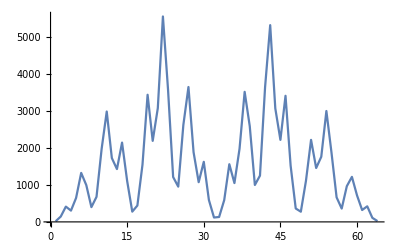

```mathematica
ListPlot[%,Joined->True]
```

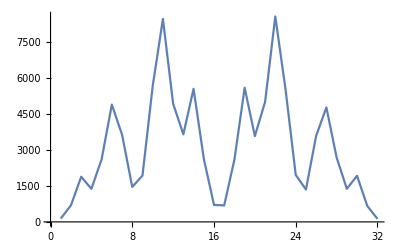

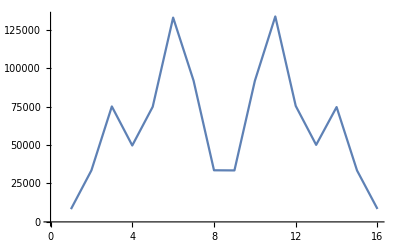

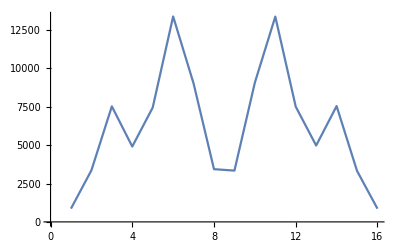

```mathematica
N[%]
```

{0.50121,0.49656,0.50054,0.49998,0.5007,0.49886,0.49913,0.49894,0.50019}

```mathematica
xdifs[l_]:=Table[BitXor[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

```mathematica
adifs[l_]:=Table[BitAnd[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

```mathematica
odifs[l_]:=Table[BitOr[l[[i]],l[[i+1]]],{i,1,Length[l]-1}]
```

```mathematica
nodifs[l_]:=Table[BitNot[BitOr[l[[i]],l[[i+1]]]],{i,1,Length[l]-1}]
```

```mathematica
zdifs[l_]:=Table[BitXor[BitNot[l[[i]]],BitNot[l[[i+1]]]],{i,1,Length[l]-1}]
```

```mathematica
a<b
a<n&&a<b
```

```mathematica
a<b<c
1≤a≤n-2&&2≤ a+1≤b≤n-1&&3≤b+1≤c≤n
```

```mathematica
a<b<c<d
1≤a≤n-3&&2≤a+1≤b≤n-2&&3≤b+1≤c≤n-1&&4≤c+1≤
```

```mathematica
Monitor[Table[Sum[Boole[(a<b)&&(b<c)&&(c>d)&&(d>e)&&(a≠c)&&(a≠d)&&(a≠e)&&(b≠d)&&(b≠e)&&(c≠e)],{a,1,mm},{b,1,mm},{c,1,mm},{d,1,mm},{e,1,mm}],{mm,5,25}],{mm,a,b,c,d,e}]
```

{6,36,126,336,756,1512,2772,4752,7722,12012,18018,26208,37128,51408,69768,93024,122094,158004,201894,255024,318780}

```mathematica
Expand[InterpolatingPolynomial[%,n]]
```

(6 n)/5+(5 n^2)/2+(7 n^3)/4+n^4/2+n^5/20

```mathematica
Reduce[a<b>c&&1≤c≤5&&1≤a≤5&&1≤b≤5&&a≠b&&b≠c&&a≠c,Integers]
```

(a==1&&b==3&&c==2)||(a==1&&b==4&&c==2)||(a==1&&b==4&&c==3)||(a==1&&b==5&&c==2)||(a==1&&b==5&&c==3)||(a==1&&b==5&&c==4)||(a==2&&b==3&&c==1)||(a==2&&b==4&&c==1)||(a==2&&b==4&&c==3)||(a==2&&b==5&&c==1)||(a==2&&b==5&&c==3)||(a==2&&b==5&&c==4)||(a==3&&b==4&&c==1)||(a==3&&b==4&&c==2)||(a==3&&b==5&&c==1)||(a==3&&b==5&&c==2)||(a==3&&b==5&&c==4)||(a==4&&b==5&&c==1)||(a==4&&b==5&&c==2)||(a==4&&b==5&&c==3)

```mathematica
FullSimplify[(1+i+k+1/2((j+k)-3)(j+k))-(1+i+1/2(j-3)j)]
```

1/2 k (-1+2 j+k)

```mathematica
a<b
b<c
(1+a),(1+a+b),(1+a+b+c)

(1+(1+a)+1/2((1+a+b)-3)(1+a+b))
(1+(1+a+b)+1/2((1+a+b+c)-3)(1+a+b+c))
```

```mathematica
FullSimplify[(1+(1+(1+a)+1/2((1+a+b)-3)(1+a+b))+1/2((1+(1+a+b)+1/2((1+a+b+c)-3)(1+a+b+c))-3)(1+(1+a+b)+1/2((1+a+b+c)-3)(1+a+b+c)))]
```

3+a+1/2 (-2+a+b) (1+a+b)+1/2 (-1+a+b+1/2 (-2+a+b+c) (1+a+b+c)) (2+a+b+1/2 (-2+a+b+c) (1+a+b+c))

```mathematica
Simplify[Reduce[{0≤a,0≤b,0≤c,3+a+1/2 (-2+a+b) (1+a+b)+1/2 (-1+a+b+1/2 (-2+a+b+c) (1+a+b+c)) (2+a+b+1/2 (-2+a+b+c) (1+a+b+c))==n},a,Integers],((C[3]|C[2]|C[1])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0)]
```

((a==8 C[3]&&b^4+c^4+32 c^3 C[3]+384 c^2 C[3]^2+b^3 (2+4 c+32 C[3])+2 c (1+64 C[3]^2+1024 C[3]^3)+8 (1+2 C[3]+24 C[3]^2+128 C[3]^3+512 C[3]^4)+b^2 (3+6 c^2+48 C[3]+384 C[3]^2+c (2+96 C[3]))+4 b (c^3+24 c^2 C[3]+8 c C[3] (1+24 C[3])+4 C[3] (3+24 C[3]+128 C[3]^2))==2 c^3+2 b (3+3 c+c^2)+8 n+48 c C[3]+c^2 (1+16 C[3]))||(a==1+8 C[3]&&b^4+c^4+c^3 (2+32 C[3])+b^3 (6+4 c+32 C[3])+c^2 (3+80 C[3]+384 C[3]^2)+b^2 (15+14 c+6 c^2+144 C[3]+96 c C[3]+384 C[3]^2)+c (2+80 C[3]+896 C[3]^2+2048 C[3]^3)+16 (1+9 C[3]+60 C[3]^2+192 C[3]^3+256 C[3]^4)+2 b (5+2 c^3+120 C[3]+576 C[3]^2+1024 C[3]^3+c^2 (5+48 C[3])+c (5+112 C[3]+384 C[3]^2))==8 n)||(a==2+8 C[3]&&b^4+c^4+2 b^3 (5+2 c+16 C[3])+c^3 (6+32 C[3])+c^2 (19+176 C[3]+384 C[3]^2)+2 c (15+200 C[3]+832 C[3]^2+1024 C[3]^3)+8 (7+70 C[3]+312 C[3]^2+640 C[3]^3+512 C[3]^4)+b^2 (39+6 c^2+240 C[3]+384 C[3]^2+c (26+96 C[3]))+2 b (31+2 c^3+312 C[3]+960 C[3]^2+1024 C[3]^3+c^2 (11+48 C[3])+c (25+208 C[3]+384 C[3]^2))==8 n)||(a==3+8 C[3]&&b^4+c^4+2 c^3 (5+16 C[3])+2 b^3 (7+2 c+16 C[3])+c^2 (47+272 C[3]+384 C[3]^2)+2 c (55+456 C[3]+1216 C[3]^2+1024 C[3]^3)+16 (11+91 C[3]+300 C[3]^2+448 C[3]^3+256 C[3]^4)+b^2 (75+6 c^2+336 C[3]+384 C[3]^2+c (38+96 C[3]))+2 b (87+2 c^3+600 C[3]+1344 C[3]^2+1024 C[3]^3+c^2 (17+48 C[3])+c (57+304 C[3]+384 C[3]^2))==8 n)||(a==4+8 C[3]&&b^4+c^4+2 c^3 (7+16 C[3])+2 b^3 (9+2 c+16 C[3])+c^2 (87+368 C[3]+384 C[3]^2)+2 c (133+808 C[3]+1600 C[3]^2+1024 C[3]^3)+16 (28+189 C[3]+492 C[3]^2+576 C[3]^3+256 C[3]^4)+b^2 (123+6 c^2+432 C[3]+384 C[3]^2+c (50+96 C[3]))+2 b (185+2 c^3+984 C[3]+1728 C[3]^2+1024 C[3]^3+c^2 (23+48 C[3])+c (101+400 C[3]+384 C[3]^2))==8 n)||(a==5+8 C[3]&&b^4+c^4+2 c^3 (9+16 C[3])+b^3 (22+4 c+32 C[3])+c^2 (139+464 C[3]+384 C[3]^2)+c (522+2512 C[3]+3968 C[3]^2+2048 C[3]^3)+8 (121+682 C[3]+1464 C[3]^2+1408 C[3]^3+512 C[3]^4)+b^2 (183+6 c^2+528 C[3]+384 C[3]^2+c (62+96 C[3]))+b (674+4 c^3+2928 C[3]+4224 C[3]^2+2048 C[3]^3+c^2 (58+96 C[3])+c (314+992 C[3]+768 C[3]^2))==8 n)||(a==6+8 C[3]&&b^4+c^4+c^3 (22+32 C[3])+b^3 (26+4 c+32 C[3])+c^2 (203+560 C[3]+384 C[3]^2)+c (902+3600 C[3]+4736 C[3]^2+2048 C[3]^3)+16 (116+559 C[3]+1020 C[3]^2+832 C[3]^3+256 C[3]^4)+b^2 (255+6 c^2+624 C[3]+384 C[3]^2+c (74+96 C[3]))+2 b (555+2 c^3+2040 C[3]+2496 C[3]^2+1024 C[3]^3+c^2 (35+48 C[3])+c (225+592 C[3]+384 C[3]^2))==8 n)||(a==7+8 C[3]&&b^4+c^4+c^3 (26+32 C[3])+b^3 (30+4 c+32 C[3])+c^2 (279+656 C[3]+384 C[3]^2)+2 c (715+2440 C[3]+2752 C[3]^2+1024 C[3]^3)+8 (407+1710 C[3]+2712 C[3]^2+1920 C[3]^3+512 C[3]^4)+b^2 (339+6 c^2+720 C[3]+384 C[3]^2+c (86+96 C[3]))+2 b (851+2 c^3+2712 C[3]+2880 C[3]^2+1024 C[3]^3+c^2 (41+48 C[3])+c (305+688 C[3]+384 C[3]^2))==8 n))&&(c==8 C[2]||c==1+8 C[2]||c==2+8 C[2]||c==3+8 C[2]||c==4+8 C[2]||c==5+8 C[2]||c==6+8 C[2]||c==7+8 C[2])&&(b==8 C[1]||b==1+8 C[1]||b==2+8 C[1]||b==3+8 C[1]||b==4+8 C[1]||b==5+8 C[1]||b==6+8 C[1]||b==7+8 C[1])

```mathematica
pairnum[{i_,j_}]:=If[i<j,(1+i+1/2(j-3)j),-(1+j+1/2(i-3)i)]
```

```mathematica
Sort[Flatten[Table[pairnum[{pairnum[{i,j}],pairnum[{j,k}]}],{i,1,10},{j,i+1,10},{k,j+1,10}],2]]
```

{2,7,12,13,22,30,31,40,41,42,56,68,69,82,83,84,98,99,100,101,121,138,139,157,158,159,178,179,180,181,201,202,203,204,205,232,255,256,280,281,282,307,308,309,310,336,337,338,339,340,367,368,369,370,371,372,407,437,438,469,470,471,503,504,505,506,539,540,541,542,543,577,578,579,580,581,582,617,618,619,620,621,622,623,667,705,706,745,746,747,787,788,789,790,831,832,833,834,835,877,878,879,880,881,882,925,926,927,928,929,930,931,975,976,977,978,979,980,981,982}

```mathematica
pairz[l_]:=Table[{l[[i]],l[[i+1]]},{i,1,Length[l]-1}]
```

```mathematica
BooleanMinimize[(a&&x1)||(!a&&!x1)]
```

(a&&x1)||(!a&&!x1)